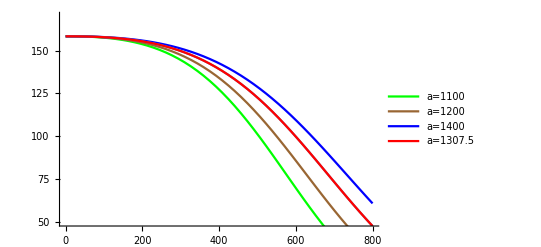

```mathematica
SetDirectory[NotebookDirectory[]];
a=1307.5;b=0.288;c=158.4;d=2.6;e=0.45;
a=1307.5;b=0.288;c=158.4;d=2.6;e=0.45;
a1=Show[Plot[c/(1+Exp[d-Log[1100/(b x)-1/b]/e]),{x,0,800},PlotLegends->{"a=1100"},PlotStyle->Green],Plot[c/(1+Exp[d-Log[1200/(b x)-1/b]/e]),{x,0,800},PlotLegends->{"a=1200"},PlotStyle->Brown],Plot[c/(1+Exp[d-Log[1400/(b x)-1/b]/e]),{x,0,800},PlotLegends->{"a=1400"},PlotStyle->Blue],Plot[c/(1+Exp[d-Log[a/(b x)-1/b]/e]),{x,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red,PlotLegends->{"a=1307.5"}],PlotRange->{{0,800},{50,170}}]
```

```mathematica
Export["./parameters/a.pdf",a1]
```

./parameters/a.pdf

```mathematica
a=1307.5;b=0.288;c=158.4;d=2.6;e=0.45;
```

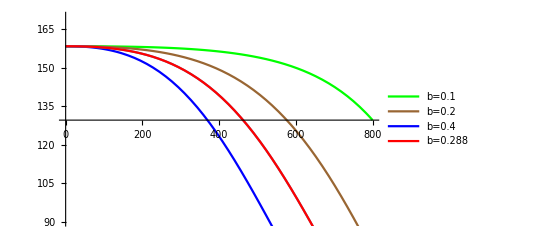

```mathematica
b1=Show[Plot[c/(1+Exp[d-Log[a/(0.1 x)-1/0.1]/e]),{x,0,800},PlotLegends->{"b=0.1"},PlotStyle->Green],Plot[c/(1+Exp[d-Log[a/(0.2 x)-1/0.2]/e]),{x,0,800},PlotLegends->{"b=0.2"},PlotStyle->Brown],Plot[c/(1+Exp[d-Log[a/(0.4 x)-1/0.4]/e]),{x,0,800},PlotLegends->{"b=0.4"},PlotStyle->Blue],Plot[c/(1+Exp[d-Log[a/(b x)-1/b]/e]),{x,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red,PlotLegends->{"b=0.288"}],PlotRange->{{0,800},{90,170}}]
```

```mathematica
Export["./parameters/b.pdf",b1]
```

./parameters/b.pdf

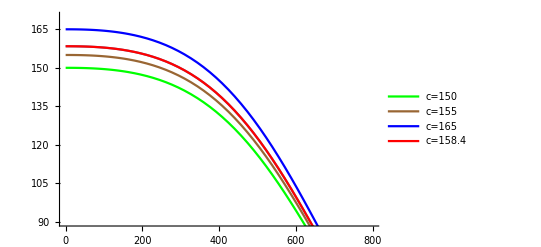

```mathematica
c1=Show[Plot[150/(1+Exp[d-Log[a/(b x)-1/b]/e]),{x,0,800},PlotLegends->{"c=150"},PlotStyle->Green],Plot[155/(1+Exp[d-Log[a/(b x)-1/b]/e]),{x,0,800},PlotLegends->{"c=155"},PlotStyle->Brown],Plot[165/(1+Exp[d-Log[a/(b x)-1/b]/e]),{x,0,800},PlotLegends->{"c=165"},PlotStyle->Blue],Plot[c/(1+Exp[d-Log[a/(b x)-1/b]/e]),{x,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red,PlotLegends->{"c=158.4"}],PlotRange->{{0,800},{90,170}}]
```

```mathematica
Export["./parameters/c.pdf",c1]
```

./parameters/c.pdf

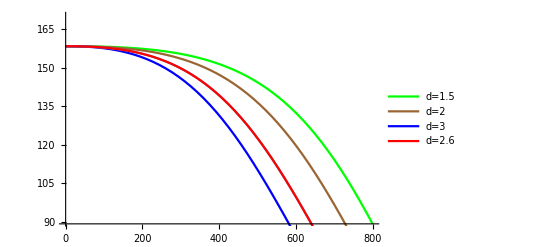

```mathematica
d1=Show[Plot[c/(1+Exp[1.5-Log[a/(b x)-1/b]/e]),{x,0,800},PlotLegends->{"d=1.5"},PlotStyle->Green],Plot[c/(1+Exp[2-Log[a/(b x)-1/b]/e]),{x,0,800},PlotLegends->{"d=2"},PlotStyle->Brown],Plot[c/(1+Exp[3-Log[a/(b x)-1/b]/e]),{x,0,800},PlotLegends->{"d=3"},PlotStyle->Blue],Plot[c/(1+Exp[d-Log[a/(b x)-1/b]/e]),{x,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red,PlotLegends->{"d=2.6"}],PlotRange->{{0,800},{90,170}}]
```

```mathematica
Export["./parameters/d.pdf",d1]
```

./parameters/d.pdf

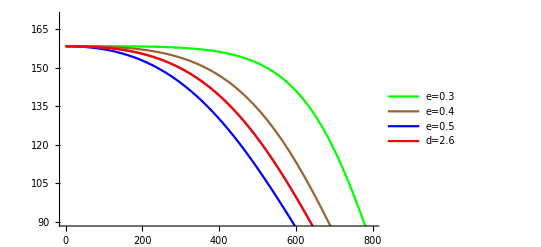

```mathematica
e1=Show[Plot[c/(1+Exp[d-Log[a/(b x)-1/b]/0.3]),{x,0,800},PlotLegends->{"e=0.3"},PlotStyle->Green],Plot[c/(1+Exp[d-Log[a/(b x)-1/b]/0.4]),{x,0,800},PlotLegends->{"e=0.4"},PlotStyle->Brown],Plot[c/(1+Exp[d-Log[a/(b x)-1/b]/0.5]),{x,0,800},PlotLegends->{"e=0.5"},PlotStyle->Blue],Plot[c/(1+Exp[d-Log[a/(b x)-1/b]/e]),{x,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red,PlotLegends->{"d=2.6"}],PlotRange->{{0,800},{90,170}}]
```

```mathematica
Export["./parameters/e.pdf",e1]
```

./parameters/e.pdf

```mathematica
Export["./parameters/func.pdf",
"Tf=c/(1 + Exp[d - FractionBox[Log[FractionBox[a, b mub] - FractionBox[1, b]], e]])"]
```

./parameters/func.pdf